## Jeremy — PS 5 — 2025-02-04

## EIWL3 Sections 14 and 17

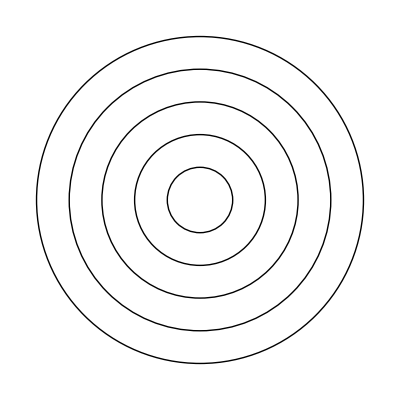

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,5}]]
```

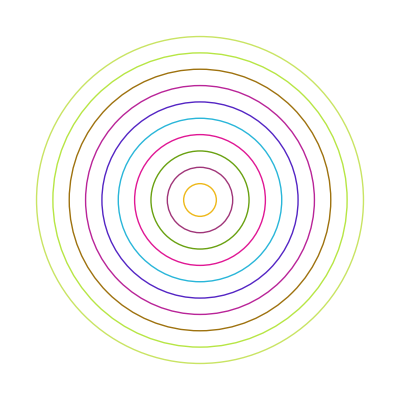

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,10}]]
```

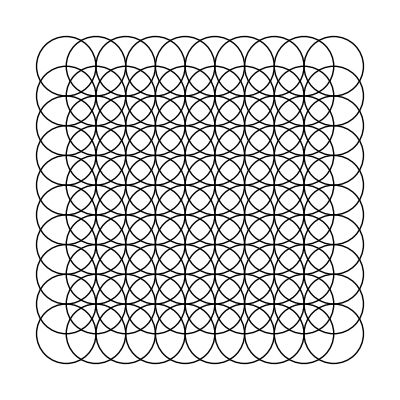

```mathematica
Graphics[Table[Circle[{x,y},1],{x,10},{y,10}]]
```

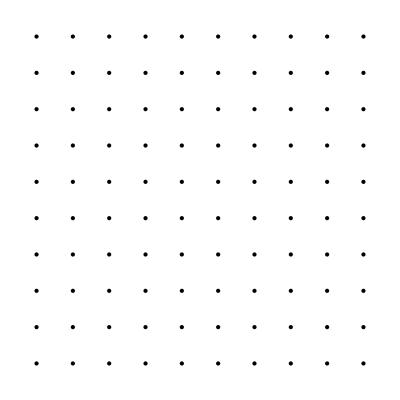

```mathematica
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,n}]],{n,1,20}]
```

```mathematica
Graphics3D[Table[Style[Sphere[{RandomInteger[10],RandomInteger[10],RandomInteger[10]}],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},0.6],RGBColor[x/11,y/11,z/11]],{x,11},{y,11},{z,11}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,10}]],{t,-2,2}]
```

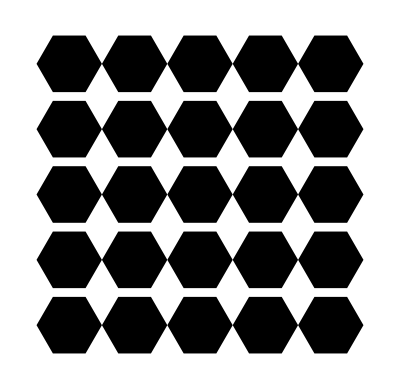

```mathematica
Graphics[Table[RegularPolygon[{x,y},1/2,6],{x,5},{y,5}]]
```

```mathematica
Graphics3D[Line[Table[{RandomInteger[50],RandomInteger[50],RandomInteger[50]},50]]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Style[Icosahedron[{0,0,0},s],Opacity[0.5]],Style[Dodecahedron[{0,0,0},1],Opacity[0.5]]}],{s,1,2}]
```

```mathematica
UnitConvert[LinguisticAssistant,"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[LinguisticAssistant,LinguisticAssistant]
```

96.963 km/h

```mathematica
UnitConvert[LinguisticAssistant["Height"],"Miles"]
```

0.205052 mi

```mathematica
LinguisticAssistant["Elevation"]/LinguisticAssistant["Height"]
```

26.8147

```mathematica
LinguisticAssistant["Mass"]/LinguisticAssistant["Mass"]
```

81.3

```mathematica
CurrencyConvert[LinguisticAssistant,"USDollars"]
```

16.44 $

```mathematica
UnitConvert[LinguisticAssistant+LinguisticAssistant+LinguisticAssistant+LinguisticAssistant,"Kilograms"]
```

305.353 kg

```mathematica
UnitConvert[{LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"],LinguisticAssistant["DistanceFromEarth"]},"LightMinutes"]
```

{11.4193 light minutes,3.66369 light minutes,0. light minutes,6.19712 light minutes,39.2376 light minutes,87.3815 light minutes,162.485 light minutes,255.371 light minutes}

```mathematica
Rotate["hello",180 Degree]
```

hello

```mathematica
Table[Rotate[Style["A",100],n Degree],{n,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate[-Graphics-,theta Degree],{theta,0,180}]
```

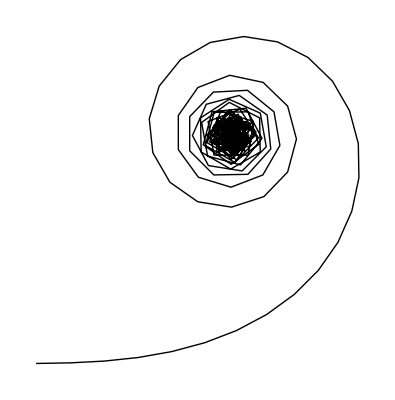

```mathematica
Graphics[Line[AnglePath[Table[angle Degree,{angle, 180}]]]]
```

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[n Degree, 100]]]],{n, 0, 360}]
```

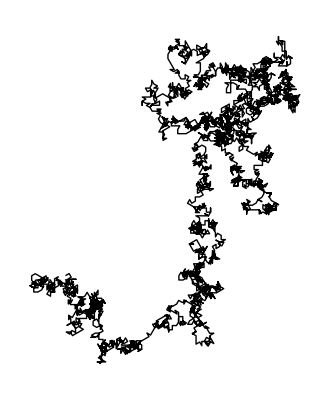

```mathematica
Graphics[Line[AnglePath[Table[Part[IntegerDigits[2^10000],n]*30 Degree,{n, Length[IntegerDigits[2^10000]]}]]]]
```